```mathematica
Clear["Global`*"];
```

Electric field equations

Equations are taken from http://www.pci.tu-bs.de/aggericke/PC4e/Kap_III/Linienbreite.htm

```mathematica
Efield[t_,ω0_,γ_,Eampl_]:=1/(2*Pi)*NIntegrate[α[ω,ω0,γ,Eampl]*Exp[I*ω*t],{ω,-10^15,10^15}];
α[ω_,ω0_,γ_,Eampl_]:=-Eampl*(1/(I*(ω0-ω)-γ)-1/(I*(ω0+ω)+γ));
```

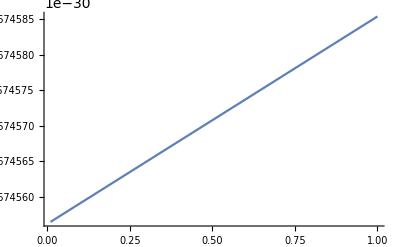

```mathematica
a1[w_]:=-1/(I*(6.50*10^14-w)-2*10^3)+-1/(I*(6.50*10^14+w)+2*10^3)-1/(I*(6.50*10^14+160*10^6-w)-2*10^3)+1/(I*(6.50*10^14+160*10^6+w)+2*10^3);
Plot[Abs[a1[w]]^2,{w,1*10^6,1*10^8}]
```